

```mathematica
Plot[x,{x,-2,2}]
```

```mathematica
y^2=x^3
```

Set::write: Tag Power in y^2 is Protected.

x^3

```mathematica
y^2==x^3
```

y^2==x^3

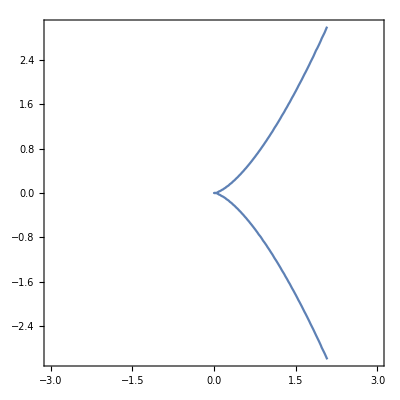

```mathematica
ContourPlot[y^2==x^3,{x,-3,3},{y,-3,3}]
```

```mathematica
{43,45,21}
```

{43,45,21}

```mathematica
1+3
```

4

```mathematica
Quantity[43,"Hours"]+Quantity[45,"Minutes"]+Quantity[21,"Seconds"]
```

157521 s

```mathematica
UnitConvert[Quantity[157521,"Seconds"],MixedUnit[{"Days","Hours","Minutes","Seconds"}]]
```

1 19

```mathematica
(Quantity[43,"Hours"]+Quantity[45,"Minutes"]+Quantity[21,"Seconds"])/2
```

157521/2 s

```mathematica
UnitConvert[Quantity[157521/2,"Seconds"],MixedUnit[{"Hours","Minutes","Seconds"}]]
```

21 52

```mathematica
PeanoCurve[1]
```

Line[{{0,0},{1,0},{2,0},{2,1},{1,1},{0,1},{0,2},{1,2},{2,2}}]

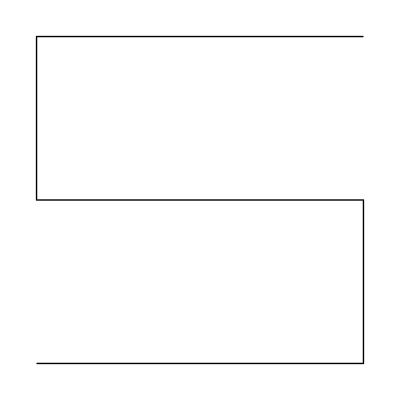

```mathematica
Graphics[PeanoCurve[1]]
```

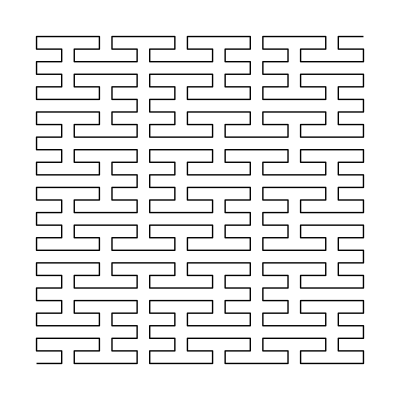

```mathematica
Graphics[PeanoCurve[3]]
```

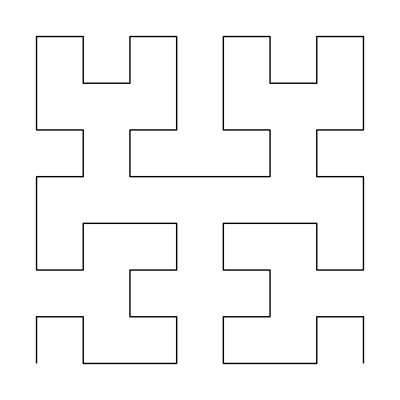

```mathematica
Graphics[HilbertCurve[3]]
```

```mathematica
FullSimplify[ArcCurvature[{x,f[x]+g[x]},x],{x,f[x],g[x]}∈Reals]
```

√((f''[x]+g''[x])^2/((1+(f'[x]+g'[x])^2)^3))

```mathematica
PowerExpand[√((f''[x]+g''[x])^2/((1+(f'[x]+g'[x])^2)^3))]
```

(f''[x]+g''[x])/((1+(f'[x]+g'[x])^2)^(3/2))

```mathematica
Apart[(f''[x]+g''[x])/((1+(f'[x]+g'[x])^2)^(3/2)),x]
```

f''[x]/((1+(f'[x]+g'[x])^2)^(3/2))+g''[x]/((1+(f'[x]+g'[x])^2)^(3/2))

```mathematica
ArcLength@HilbertCurve[3]
```

63

```mathematica
(f''[x]+g''[x])((1+(f'[x]+g'[x])^2)^(3/2))^-1
```

(f''[x]+g''[x])/((1+(f'[x]+g'[x])^2)^(3/2))

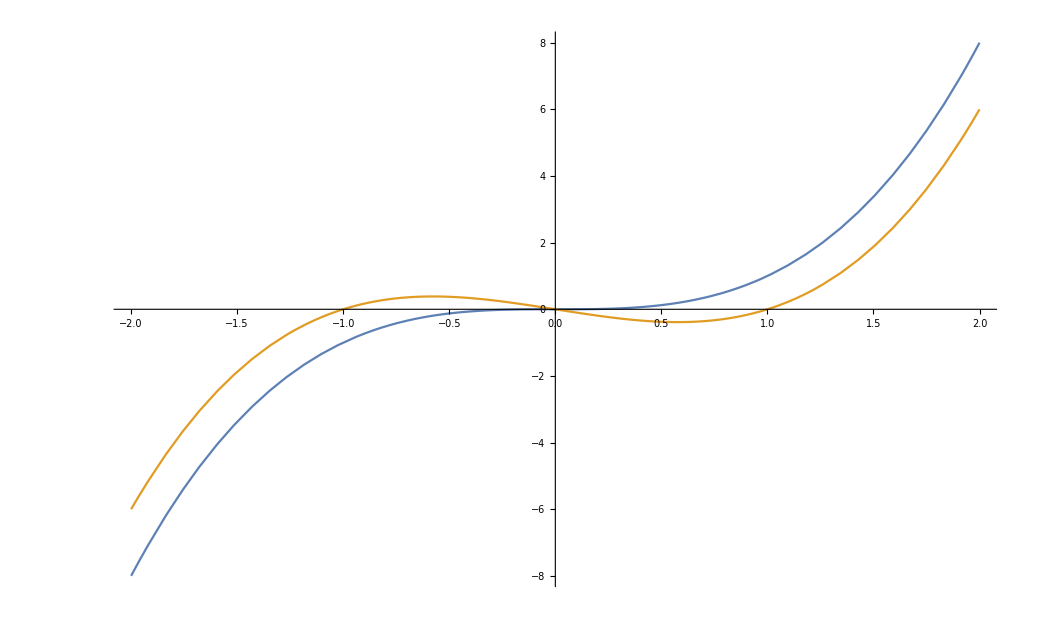

```mathematica
Plot[{x^3,x^3-x},{x,-2,2}]
```

```mathematica
FullSimplify[Map[ArcCurvature[{x,#},x]&,{x^3,x^3-x}],x∈Reals]
```

{(6 Abs[x])/((1+9 x^4)^(3/2)),(6 Abs[x])/((2-6 x^2+9 x^4)^(3/2))}

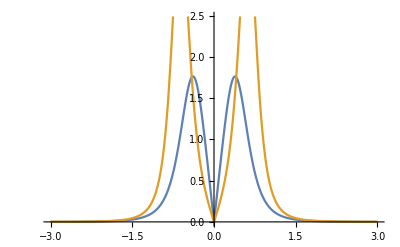

```mathematica
Plot[{(6 Abs[x])/((1+9 x^4)^(3/2)),(6 Abs[x])/((2-6 x^2+9 x^4)^(3/2))},{x,-3,3}]
```

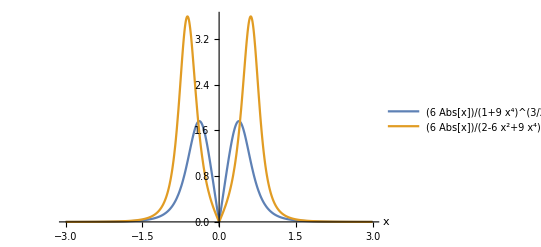

```mathematica
Plot[{(6 Abs[x])/((1+9 x^4)^(3/2)),(6 Abs[x])/((2-6 x^2+9 x^4)^(3/2))},{x,-3,3},PlotRange->Full,PlotLegends->"Expressions",AxesLabel->Automatic]
```

```mathematica
FullSimplify[ArcCurvature[{x,x^3-α x},x],{x,α}∈Reals]
```

(6 Abs[x])/((1+(-3 x^2+α)^2)^(3/2))

```mathematica
Manipulate[Plot[(6 Abs[x])/((1+(-3 x^2+α)^2)^(3/2)),{x,-0.30054153769202274,0.30054153769202274}],{α,-0.45639571051034683,0.45639571051034683}]
```

```mathematica
Manipulate[Plot[(6 Abs[x])/((1+(-3 x^2+α)^2)^(3/2)),{x,-5,5}],{α,-5,5}]
```

```mathematica
Manipulate[
Plot[(6 Abs[x])/((1+(-3 x^2+α)^2)^(3/2)),{x,-5,5},PlotRange->Full,PlotLegends->"Expressions",AxesLabel->Automatic,ColorFunction->"DarkRainbow"]
,{α,-5,5}]
```

```mathematica
Manipulate[
Plot[(6 Abs[x])/((1+(-3 x^2+α)^2)^(3/2)),{x,-5,5},PlotRange->{0,10},PlotLegends->"Expressions",AxesLabel->Automatic,ColorFunction->"DarkRainbow"]
,{α,-5,5}]
```

```mathematica
FullSimplify[Normalize@{x,-x}.Normalize@{x,x^3},x∈Reals]
```

-(-1+x^2)/(√2 √(1+x^4))

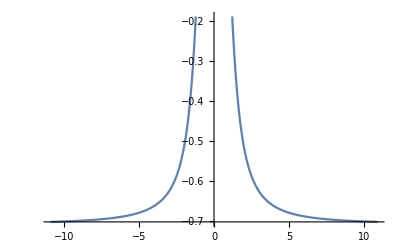

```mathematica
Plot[-(-1+x^2)/(√2 √(1+x^4)),{x,-10.92,10.92}]
```

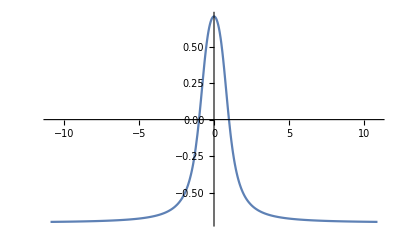

```mathematica
Plot[-(-1+x^2)/(√2 √(1+x^4)),{x,-10.92,10.92},PlotRange->Full]
```

```mathematica
FullSimplify[Normalize@{x,α x}.Normalize@{x,x^3},x∈Reals]
```

(x^2+x^4 α)/(√((x^4+x^8) (1+Abs[α]^2)))

```mathematica
FullSimplify[Normalize@{x,α x}.Normalize@{x,x^3},{α,x}∈Reals]
```

(1+x^2 α)/(√((1+x^4) (1+α^2)))

```mathematica
FullSimplify[Normalize@D[{x,-x},x].Normalize@D[{x,x^3},x],x∈Reals]
```

(1-3 x^2)/(√(2+18 x^4))

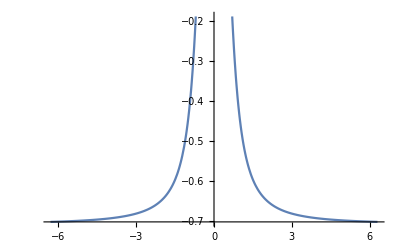

```mathematica
Plot[(1-3 x^2)/(√(2+18 x^4)),{x,-6.304664939550714,6.304664939550714}]
```

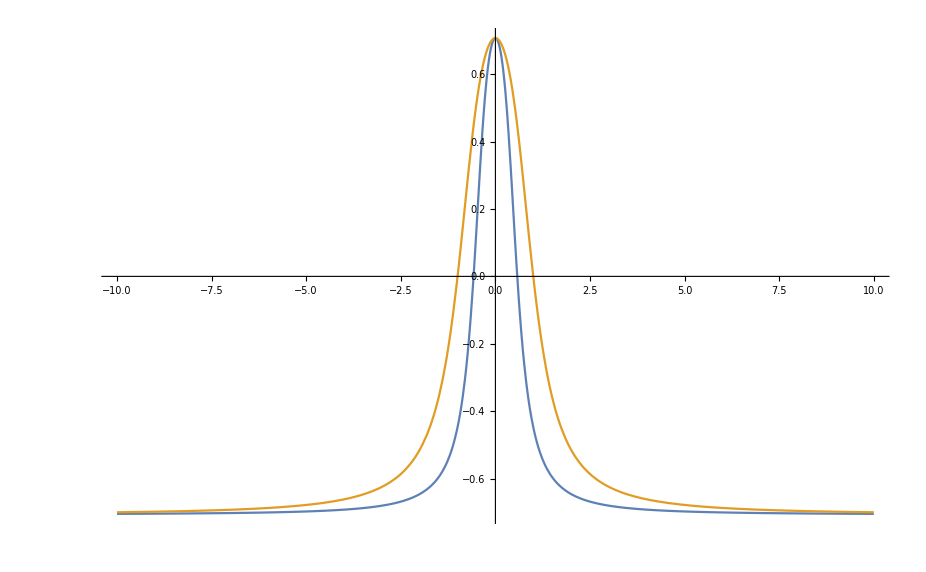

```mathematica
Plot[{(1-3 x^2)/(√(2+18 x^4)),-(-1+x^2)/(√2 √(1+x^4))},{x,-10,10},PlotRange->Full]
```

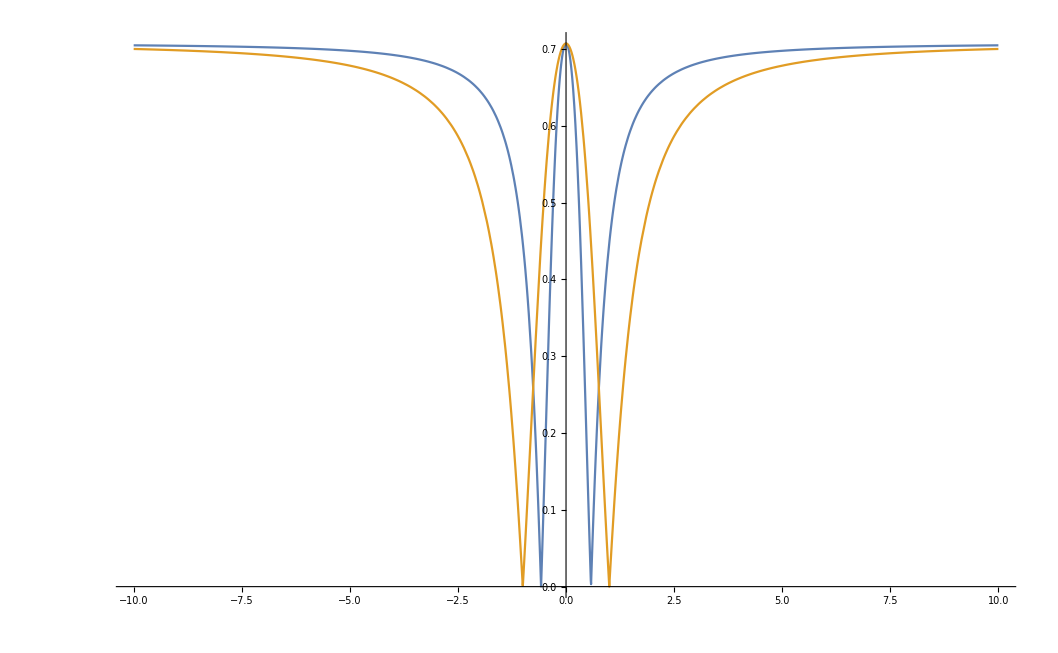

```mathematica
Plot[{Abs[(1-3 x^2)/(√(2+18 x^4))],Abs[-(-1+x^2)/(√2 √(1+x^4))]},{x,-10,10},PlotRange->Full]
```

```mathematica
(1+x^2 α)/(√((1+x^4) (1+α^2)))
```

(1+x^2 α)/(√((1+x^4) (1+α^2)))

```mathematica
Manipulate[Plot[(1+x^2 α)/(√((1+x^4) (1+α^2))),{x,-1.0602878999079475,1.0602878999079475}],{α,-1.2863733215943343,1.2863733215943343}]
```

```mathematica
With[{a=5},
Manipulate[
Plot[(1+x^2 α)/(√((1+x^4) (1+α^2))),{x,-a,a}]
,{α,-a,a}]
]
```

```mathematica
FunctionPeriod[x^3]
```

FunctionPeriod::argtu: FunctionPeriod called with 1 argument; 2 or 3 arguments are expected.

FunctionPeriod[x^3]

```mathematica
FunctionPeriod[x^3,x,Reals]
```

0

```mathematica
27 365
```

9855